4982.52

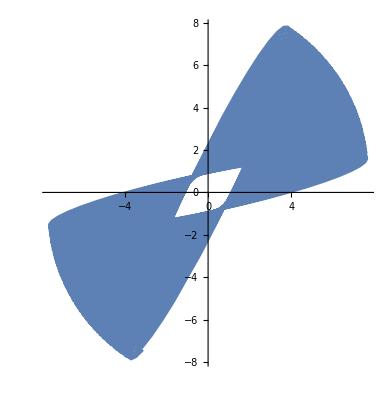

```mathematica
(*for a sphere, c ~.64*)
l = 40;
densityOfSand = 1600;
radiusOfCylinder= 1;
heightOfSand = .5;
radiusOfOraface = .1;
areaOfOraface=π*(radiusOfOraface)^2;
c=.58;
g=9.8;
initalMass=π*(radiusOfBall^2)*heightOfSand*densityOfSand;
massFlow= -c*densityOfSand*√g*(areaOfOraface-1.5*.0000625)^(5/2);
r={l*Sin[θ[t]]*Cos[ϕ[t]],l*Sin[θ[t]]*Sin[ϕ[t]],-l*Cos[θ[t]]};
v=FullSimplify[TrigReduce[D[r,t]]];
v2=FullSimplify[TrigReduce[v.v]];
U=(initalMass+massFlow*t)*g*r[[3]];
T=.5*(initalMass+massFlow*t)*v2;
L=T-U;
theq=TrigReduce[D[D[L,θ'[t]],t]-D[L,θ[t]]];
phiq=TrigReduce[D[D[L,ϕ'[t]],t]-D[L,ϕ[t]]];
tmax=1000;
initalMass/-massFlow
If[initalMass/-massFlow>tmax,
sol1=NDSolve[{theq==0,phiq==0,θ'[0]== 0,ϕ'[0]== √(g/l*ArcCos[θ[0]])*.1,θ[0]== π/16,ϕ[0]==π/16},{θ,ϕ},{t,0,tmax}];
solθ[t_]:=θ[t]/.sol1[[1]][[1]];
x[t_]:=l*Sin[solθ[t]]*Cos[solϕ[t]];
y[t_]:=l*Sin[solθ[t]]*Sin[solϕ[t]];
ParametricPlot[{x[t],y[t]},{t,.1,tmax}],Abort[]]
```